```mathematica
trikotnik={{0,0},{5,1},{7,4}}
Stranice[{}]
```

{{0,0},{5,1},{7,4}}

Stranice[{}]

```mathematica
Stranice[{AA_,BB_,CC_}]:={{BB,CC},{CC,AA},{AA,BB}}
```

```mathematica
Koti[{AA_,BB_,CC_}]:={{CC,AA,BB},{AA,BB,CC},{BB,CC,AA}}
```

```mathematica
SlikaOglisc[trikotnik_]:=Map[Point,trikotnik]
```

```mathematica
SlikaStranic[trikotnik_]:=Map[Line,Stranice[trikotnik]]

Stranice[trikotnik]
```

{{{5,1},{7,4}},{{7,4},{0,0}},{{0,0},{5,1}}}

```mathematica
Koti[trikotnik]
```

{{{7,4},{0,0},{5,1}},{{0,0},{5,1},{7,4}},{{5,1},{7,4},{0,0}}}

{{{7,4},{0,0},{5,1}},{{0,0},{5,1},{7,4}},{{5,1},{7,4},{0,0}}}

```mathematica
Graphics[SlikaOglisc[trikotnik]]
```

-Graphics-

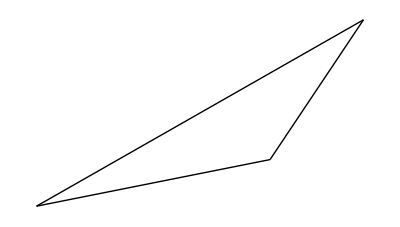

```mathematica
Graphics[SlikaStranic[trikotnik]]
```

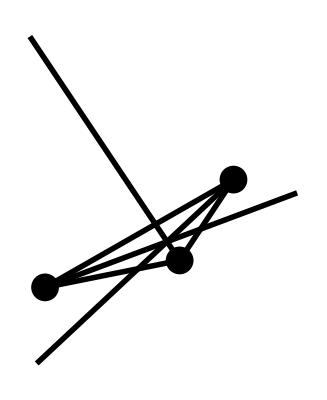

```mathematica
Graphics[{PointSize[0.05],Thickness[0.01],SlikaOglisc[trikotnik],SlikaStranic[trikotnik],Line[SimetralaKota[alfa]],Line[SimetralaKota[beta]],Line[SimetralaKota[gama]]}]
```

```mathematica
VektorSimetraleKota[{x_,y_,z_}]:=Normalize[Normalize[x-y]+Normalize[z-y]]
```

```mathematica
SimetralaKota[{x_,y_,z_},dol_:10]:={y,y+VektorSimetraleKota[{x,y,z}]*dol}
```

```mathematica
VektorSimetraleKota[Koti[trikotnik][[1]]]//N
```

{0.936505,0.350655}

```mathematica
alfa=Koti[trikotnik][[1]]
```

{{7,4},{0,0},{5,1}}

```mathematica
VektorSimetraleKota[alfa]//N
```

{0.936505,0.350655}

```mathematica
SimetralaKota[alfa]//N
```

{{0.,0.},{9.36505,3.50655}}

```mathematica
beta=Koti[trikotnik][[2]]
```

{{0,0},{5,1},{7,4}}

```mathematica
gama=Koti[trikotnik][[3]]
```

{{5,1},{7,4},{0,0}}

```mathematica
Map[Map[SimetralaKota,Koti[trikotnik]]]
```

Map[{{{0,0},{(10 (5/(√26)+7/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2)),(10 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))}},{{5,1},{5+(10 (2/(√13)-5/(√26)))/(√((3/(√13)-1/(√26))^2+(-2/(√13)+5/(√26))^2)),1+(10 (3/(√13)-1/(√26)))/(√((3/(√13)-1/(√26))^2+(-2/(√13)+5/(√26))^2))}},{{7,4},{7+(10 (-2/(√13)-7/(√65)))/(√((3/(√13)+4/(√65))^2+(2/(√13)+7/(√65))^2)),4+(10 (-3/(√13)-4/(√65)))/(√((3/(√13)+4/(√65))^2+(2/(√13)+7/(√65))^2))}}}]

```mathematica
Graphics[{PointSize[0.05],Thickness[0.01],SlikaOglisc[trikotnik],SlikaStranic[trikotnik],Map[Line,Map[SimetralaKota,Koti[trikotnik]]]}]
```

-Graphics-